# Manual Implementation and Test of a Random Number Generator

## Milan Cvitkovic

## a) The Lehmer Minimal Standard - Code Implementation

Writing a module to generate a random number based on the Lehmer minimal standard pseud-random number generating function z+1 = f(z) = 16807z mod 2147483647 (code derived from Bill Titus’ lecture):

```mathematica
minStandardRNG[]:=
Module[
{a=16807,m=2147483647},

seed=Mod[a*seed,m];
N[seed/m]
]
```

Testing based on test from Park and Miller page 1195 (code has to be modified slightly to output integers and not values between 0 and 1 to see if the code passes the test):

```mathematica
Clear[n,seed]
minStandardRNG[]:=
Module[
{a=16807,m=2147483647},

seed=Mod[a*seed,m];
N[seed/m]
]
n=1;
For[i=1,i≤10000,i++,
(
n=minStandardRNGTest[n]
)
]
n
```

1.04362×10^9

Mathematica seems to be rounding this number, but it is unclear whether it is actually rounding in memory or just displaying a rounded number.  The number seems to be correct, however.

## b) Time Comparison Between Lehmer Minimal Standard RNG and Mathematica’s RandomReal[]

Comparing how long it takes the Lehmer RNG coded above to calculate a random number vs. Mathematica’s RandomReal[], both using the same seed:

```mathematica
Clear[seed]
seed=9890;
Timing[minStandardRNG[]]
seed=9890;SeedRandom[seed];
Timing[RandomReal[]]
```

{0.000046,0.0774028}

{7.×10^-6,0.882576}

Thus we can see that RandomReal is faster by about a factor of 10

## c) Sub-Standard Lehmer RNG

Using the same module code from our Lehmer RNG but with the sub-standard values a=78 and m=127:

```mathematica
seed=1
subStandardRNG[]:=
Module[
{a=78,m=127},

seed=Mod[a*seed,m];
N[seed/m]
]
```

1

We can show that this RNG is sub-standard by cycling through the sequence 400 times and seeing that the period is 126:

{0.614173,0.905512,0.629921,0.133858,0.440945,0.393701,0.708661,0.275591,0.496063,0.692913,0.0472441,0.685039,0.433071,0.779528,0.80315,0.645669,0.362205,0.251969,0.653543,0.976378,0.15748,0.283465,0.110236,0.598425,0.677165,0.818898,0.874016,0.173228,0.511811,0.92126,0.858268,0.944882,0.700787,0.661417,0.590551,0.0629921,0.913386,0.244094,0.0393701,0.0708661,0.527559,0.149606,0.669291,0.204724,0.968504,0.543307,0.377953,0.480315,0.464567,0.23622,0.425197,0.165354,0.897638,0.015748,0.228346,0.811024,0.259843,0.267717,0.88189,0.787402,0.417323,0.551181,0.992126,0.385827,0.0944882,0.370079,0.866142,0.559055,0.606299,0.291339,0.724409,0.503937,0.307087,0.952756,0.314961,0.566929,0.220472,0.19685,0.354331,0.637795,0.748031,0.346457,0.023622,0.84252,0.716535,0.889764,0.401575,0.322835,0.181102,0.125984,0.826772,0.488189,0.0787402,0.141732,0.0551181,0.299213,0.338583,0.409449,0.937008,0.0866142,0.755906,0.96063,0.929134,0.472441,0.850394,0.330709,0.795276,0.0314961,0.456693,0.622047,0.519685,0.535433,0.76378,0.574803,0.834646,0.102362,0.984252,0.771654,0.188976,0.740157,0.732283,0.11811,0.212598,0.582677,0.448819,0.00787402,0.614173,0.905512,0.629921,0.133858,0.440945,0.393701,0.708661,0.275591,0.496063,0.692913,0.0472441,0.685039,0.433071,0.779528,0.80315,0.645669,0.362205,0.251969,0.653543,0.976378,0.15748,0.283465,0.110236,0.598425,0.677165,0.818898,0.874016,0.173228,0.511811,0.92126,0.858268,0.944882,0.700787,0.661417,0.590551,0.0629921,0.913386,0.244094,0.0393701,0.0708661,0.527559,0.149606,0.669291,0.204724,0.968504,0.543307,0.377953,0.480315,0.464567,0.23622,0.425197,0.165354,0.897638,0.015748,0.228346,0.811024,0.259843,0.267717,0.88189,0.787402,0.417323,0.551181,0.992126,0.385827,0.0944882,0.370079,0.866142,0.559055,0.606299,0.291339,0.724409,0.503937,0.307087,0.952756,0.314961,0.566929,0.220472,0.19685,0.354331,0.637795,0.748031,0.346457,0.023622,0.84252,0.716535,0.889764,0.401575,0.322835,0.181102,0.125984,0.826772,0.488189,0.0787402,0.141732,0.0551181,0.299213,0.338583,0.409449,0.937008,0.0866142,0.755906,0.96063,0.929134,0.472441,0.850394,0.330709,0.795276,0.0314961,0.456693,0.622047,0.519685,0.535433,0.76378,0.574803,0.834646,0.102362,0.984252,0.771654,0.188976,0.740157,0.732283,0.11811,0.212598,0.582677,0.448819,0.00787402,0.614173,0.905512,0.629921,0.133858,0.440945,0.393701,0.708661,0.275591,0.496063,0.692913,0.0472441,0.685039,0.433071,0.779528,0.80315,0.645669,0.362205,0.251969,0.653543,0.976378,0.15748,0.283465,0.110236,0.598425,0.677165,0.818898,0.874016,0.173228,0.511811,0.92126,0.858268,0.944882,0.700787,0.661417,0.590551,0.0629921,0.913386,0.244094,0.0393701,0.0708661,0.527559,0.149606,0.669291,0.204724,0.968504,0.543307,0.377953,0.480315,0.464567,0.23622,0.425197,0.165354,0.897638,0.015748,0.228346,0.811024,0.259843,0.267717,0.88189,0.787402,0.417323,0.551181,0.992126,0.385827,0.0944882,0.370079,0.866142,0.559055,0.606299,0.291339,0.724409,0.503937,0.307087,0.952756,0.314961,0.566929,0.220472,0.19685,0.354331,0.637795,0.748031,0.346457,0.023622,0.84252,0.716535,0.889764,0.401575,0.322835,0.181102,0.125984,0.826772,0.488189,0.0787402,0.141732,0.0551181,0.299213,0.338583,0.409449,0.937008,0.0866142,0.755906,0.96063,0.929134,0.472441,0.850394,0.330709,0.795276,0.0314961,0.456693,0.622047,0.519685,0.535433,0.76378,0.574803,0.834646,0.102362,0.984252,0.771654,0.188976,0.740157,0.732283,0.11811,0.212598,0.582677,0.448819,0.00787402,0.614173,0.905512,0.629921,0.133858,0.440945,0.393701,0.708661,0.275591,0.496063,0.692913,0.0472441,0.685039,0.433071,0.779528,0.80315,0.645669,0.362205,0.251969,0.653543,0.976378,0.15748,0.283465}

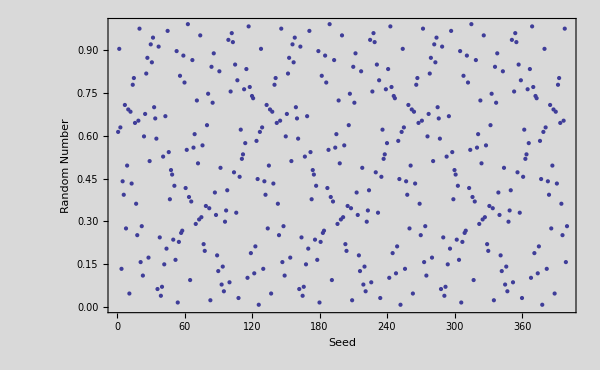

0.614173

0.614173

```mathematica
Clear[seed]
seed=1;
data01 = Table[subStandardRNG[],{400}]
ListPlot[data01,Frame -> True, ImageSize -> 600, Background -> LightGray,GridLines->Automatic,FrameLabel -> {"Seed","Random Number","Plot of Sub-Standard Lehmer RNG values for seeds 1 through 400"}]
data01[[1]]
data01[[127]]
```

It is hard to see directly in the data, but using the plot to guide us we can see that the sub standard RNG starts returning similar values at around 100.  If we delve into the table we eventually run into the 126th output, which is the same as the first output.  Thus the period is

We can also find the period by generating a random walk using the sub standard RNG (random walk code taken from Bill Titus’ WK01 Notebook):

```mathematica
Clear[steps,xValues,tValues,rwList,seed]
seed=1;
steps[n_]:=Table[2 subStandardRNG[]-1,{n}];
xValues[n_]:=FoldList[Plus,0,steps[n]];
tValues[n_]:=Table[i,{i,0,n}];
rwList[n_]:=Transpose[{tValues[n],xValues[n]}];
```

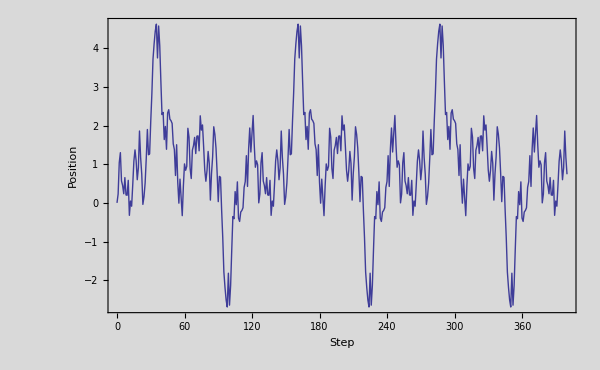

```mathematica
data02 = rwList[400];
ListPlot[data02,Frame -> True, ImageSize -> 600, Background -> LightGray,GridLines->Automatic,FrameLabel -> {"Step","Position","Plot of 400 step random walk using sub-standard RNG"},Joined->True]
```

In addition to once again seeing that the function has a period of 126, it should be noted that there appears to be some kind of inversion event happening somewhere in period, as can be seen by the two very large and suspiciously symmetrical peaks at around 40 and 100.  That, in addition to the fact that the size of these peaks indicates that the RNG gave a number greater than or less than 0.5 almost 15 times in row, seems to indicate that this RNG has flaws beyond its short period.

## d) Chi Square Test

We will now assess the randomness of each of the three RNGs we have discussed - minStandardRNG, RandomReal, and subStandardRNG - using a chi-square test.

First, finding the distribution of values between 0 and 1 generated by these RNGs, with 100 bins between 0 and 1:

```mathematica
minStandardBins=BinCounts[Table[minStandardRNG[],{10000}],{0,1,0.01}]
randomRealBins=BinCounts[Table[RandomReal[],{10000}],{0,1,0.01}]
subStandardBins=BinCounts[Table[subStandardRNG[],{10000}],{0,1,0.01}]
```

{106,91,106,89,104,105,95,76,99,99,103,101,100,99,85,104,115,96,106,81,102,117,110,84,88,94,84,92,101,95,89,108,107,105,100,94,101,96,121,90,110,106,96,103,93,101,91,91,122,112,105,81,107,102,85,101,90,88,94,90,96,105,93,107,94,129,108,99,102,104,95,91,121,99,115,107,109,97,88,103,113,108,92,102,103,105,113,123,106,84,108,100,94,94,101,108,98,82,98,100}

{94,113,98,100,107,118,101,107,97,114,93,100,92,109,79,102,73,107,92,91,105,94,97,104,106,105,103,100,100,86,95,114,111,101,111,95,86,98,114,88,94,114,100,111,94,94,85,111,106,91,96,118,97,102,101,121,118,74,103,104,106,84,87,87,100,87,104,77,99,104,102,97,104,95,111,89,96,94,111,109,111,107,97,99,104,102,95,112,91,108,101,97,98,99,96,101,83,110,92,120}

{80,79,79,159,79,80,79,159,80,79,80,159,80,80,159,79,79,79,160,79,79,80,158,79,79,158,79,79,79,159,79,79,80,160,79,79,79,158,79,79,160,79,79,79,160,80,79,80,159,79,79,159,79,80,79,158,79,80,80,158,79,80,160,79,79,79,158,79,79,79,158,79,79,80,159,80,80,159,79,80,79,158,80,80,79,159,79,79,159,79,80,79,159,80,79,79,159,79,80,79}

Next, writing a module chiSquare[binList,M,N] which will return the chi-square value for a list of bin counts:

```mathematica
chiSquare[binList_,n_]:=
Module[
{chiSquare=1,i},

For[i=1,i<=Length[binList],i++,
(chiSquare=chiSquare+((binList[[i]]-n/Length[binList])^2/(n/Length[binList]))
)
];

N[chiSquare]
]
```

Finding chi-square for each of the three RNGs:

```mathematica
chiSquare[minStandardBins,10000]
chiSquare[randomRealBins,10000]
chiSquare[subStandardBins,10000]
```

100.06

98.98

1219.56

Now checking to see whether the value of chi-squared/number of bins lies on the interval {1-2/m^(1/2),1+2/m^(1/2)}, which is the official chi-square test:

```mathematica
chiSquare[minStandardBins,10000]/100>(1-2/10)&&chiSquare[minStandardBins,10000]/100<(1+2/10)
chiSquare[randomRealBins,10000]/100>(1-2/10)&&chiSquare[randomRealBins,10000]/100<(1+2/10)
chiSquare[subStandardBins,10000]/100>(1-2/10)&&chiSquare[subStandardBins,10000]/100<(1+2/10)
```

True

True

False

Thus we see that the Lehmer minimum standard RNG and Mathematica’s RandomReal both pass the chi-square test, but the sub-standard Lehmer RNG does not.